```mathematica
(*f[x_]=ⅇ^x Sin[2 x];*)
f[x_]=ArcSin[x^2/(x^2+1)]
df[x_]=D[f[x], x];
h=0.1;
der[x_]=(f[x+h]-f[x])/h
der2[x_]=(-f[x+2 h]+4f[x+h]-3f[x])/(2 h)
der3[x_]=(f[x-2 h]-8f[x-h]+8f[x+h]-f[x+2 h])/(12 h);
df[0.75]//N
```

ArcSin[x^2/(1+x^2)]

10. (-ArcSin[x^2/(1+x^2)]+ArcSin[(0.1+x)^2/(1+(0.1+x)^2)])

5. (-3 ArcSin[x^2/(1+x^2)]+4 ArcSin[(0.1+x)^2/(1+(0.1+x)^2)]-ArcSin[(0.2+x)^2/(1+(0.2+x)^2)])

0.658555

```mathematica
der[0.75]//N
der2[0.75]//N
der3[0.75]//N
```

0.645698

0.661461

0.658612

```mathematica
e[x_]=Abs[(df[0.75]-der[0.75])/df[0.75]*100]
```

1.95226

```mathematica
e[x_]=Abs[(df[0.75]-der2[0.75])/df[0.75]*100]
```

0.441324

```mathematica
e[x_]=Abs[(df[0.75]-der3[0.75])/df[0.75]*100]
```

0.00874623

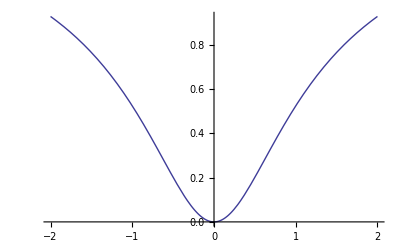

```mathematica
Plot[f[x],{x,-2,2}]
```